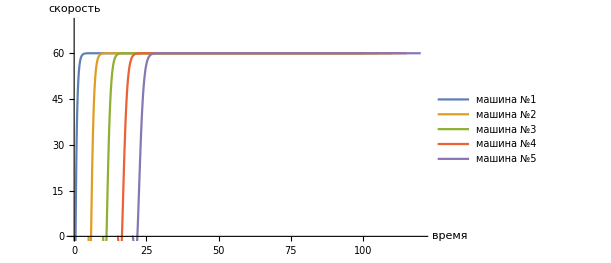

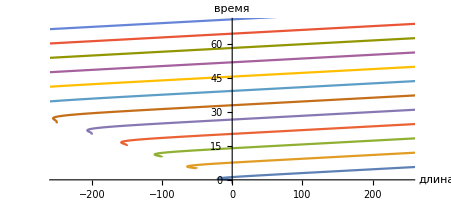

```mathematica
dx0=60;
x0 = 0;
τ = 5;
tt= 120;
dStart = 2;
λ= 50;
tmax =120;

qqq[t_] := If[t <= tt, dx0 *t,dx0*tt];
Module[{solF, solS, solT, u,  v,  w, t},

solF = NDSolve[{u'[t]==dStart* (Evaluate[qqq[t]]  -u[t]-λ), u[t /; t≤ 0] == -0*λ},u,{t,0 ,tmax}];
solS = NDSolve[{v'[t]==dStart* (Evaluate[u[t-τ] /.solF][[1]]-v[t]-λ), v[t /; t≤ τ ] == -1*λ},v,{t,τ,tmax}];
solT = NDSolve[{w'[t]== dStart* (Evaluate[v[t-τ] /.solS][[1]]-w[t]-λ), w[t /; t≤ 2*τ ] == -2*λ},w,{t,2*τ  ,tmax}];
sol4 = NDSolve[{p'[t]==dStart* (Evaluate[w[t-τ] /.solT][[1]]-p[t]-λ), p[t /; t≤ 3*τ ] == -3*λ},p,{t,3*τ  ,tmax}];
sol5 = NDSolve[{g'[t]==dStart* (Evaluate[p[t-τ] /.sol4][[1]]-g[t]-λ), g[t /; t≤ 4*τ ] == -4*λ},g,{t,4*τ  ,tmax}];
ParametricPlot[{Evaluate[{t-4*τ,u'[t-4*τ]} /. solF],Evaluate[{t-3*τ,v'[t-3*τ]} /. solS],Evaluate[{t-2*τ,w'[t-2*τ]} /. solT],Evaluate[{t-τ,p'[t-τ]} /. sol4],Evaluate[{t,g'[t]} /. sol5]},{t,4*τ,tmax}, PlotRange->{{0,tmax},{0,dx0+10}},AxesLabel->{время,скорость},PlotLegends->Placed[{"машина №1","машина №2","машина №3","машина №4","машина №5"},{Right,Center}]]]
Module[{solF, solS, solT, u,  v,  w, t},

solF = NDSolve[{u'[t]==dStart* (Evaluate[qqq[t]]  -u[t]-λ), u[t /; t≤ 0] == -0*λ},u,{t,0 ,tmax}];
solS = NDSolve[{v'[t]==dStart* (Evaluate[u[t-τ] /.solF][[1]]-v[t]-λ), v[t /; t≤ τ ] == -1*λ},v,{t,τ,tmax}];
solT = NDSolve[{w'[t]== dStart* (Evaluate[v[t-τ] /.solS][[1]]-w[t]-λ), w[t /; t≤ 2*τ ] == -2*λ},w,{t,2*τ  ,tmax}];
sol4 = NDSolve[{p'[t]==dStart* (Evaluate[w[t-τ] /.solT][[1]]-p[t]-λ), p[t /; t≤ 3*τ ] == -3*λ},p,{t,3*τ  ,tmax}];
sol5 = NDSolve[{g'[t]==dStart* (Evaluate[p[t-τ] /.sol4][[1]]-g[t]-λ), g[t /; t≤ 4*τ ] == -4*λ},g,{t,4*τ  ,tmax}];
sol6 = NDSolve[{g6'[t]==dStart* (Evaluate[g[t-τ] /.sol5][[1]]-g6[t]-λ), g6[t /; t≤ 5*τ ] == -5*λ},g6,{t,5*τ  ,tmax}];
sol7 = NDSolve[{g7'[t]==dStart* (Evaluate[g6[t-τ] /.sol6][[1]]-g7[t]-λ), g7[t /; t≤ 6*τ ] == -6*λ},g7,{t,6*τ  ,tmax}];
sol8 = NDSolve[{g8'[t]==dStart* (Evaluate[g7[t-τ] /.sol7][[1]]-g8[t]-λ), g8[t /; t≤ 7*τ ] == -7*λ},g8,{t,7*τ  ,tmax}];
sol9 = NDSolve[{g9'[t]==dStart* (Evaluate[g8[t-τ] /.sol8][[1]]-g9[t]-λ), g9[t /; t≤ 8*τ ] == -8*λ},g9,{t,8*τ  ,tmax}];
sol10 = NDSolve[{g10'[t]==dStart* (Evaluate[g9[t-τ] /.sol9][[1]]-g10[t]-λ), g10[t /; t≤ 9*τ ] == -9*λ},g10,{t,9*τ  ,tmax}];
sol11 = NDSolve[{g11'[t]==dStart* (Evaluate[g10[t-τ] /.sol10][[1]]-g11[t]-λ), g11[t /; t≤ 10*τ ] == -10*λ},g11,{t,10*τ  ,tmax}];
sol12 = NDSolve[{g12'[t]==dStart* (Evaluate[g11[t-τ] /.sol11][[1]]-g12[t]-λ), g12[t /; t≤ 11*τ ] == -11*λ},g12,{t,11*τ  ,tmax}];
sol13 = NDSolve[{g13'[t]==dStart* (Evaluate[g12[t-τ] /.sol12][[1]]-g13[t]-λ), g13[t /; t≤ 12*τ ] == -12*λ},g13,{t,12*τ  ,tmax}];
sol14 = NDSolve[{g14'[t]==dStart* (Evaluate[g13[t-τ] /.sol13][[1]]-g14[t]-λ), g14[t /; t≤ 13*τ ] == -13*λ},g14,{t,13*τ  ,tmax}];
sol15 = NDSolve[{g15'[t]==dStart* (Evaluate[g14[t-τ] /.sol14][[1]]-g15[t]-λ), g15[t /; t≤ 14*τ ] == -14*λ},g15,{t,14*τ  ,tmax}];
sol16 = NDSolve[{g16'[t]==dStart* (Evaluate[g15[t-τ] /.sol15][[1]]-g16[t]-λ), g16[t /; t≤ 15*τ ] == -15*λ},g16,{t,15*τ  ,tmax}];
sol17 = NDSolve[{g17'[t]==dStart* (Evaluate[g16[t-τ] /.sol16][[1]]-g17[t]-λ), g17[t /; t≤ 16*τ ] == -16*λ},g17,{t,16*τ  ,tmax}];
sol18 = NDSolve[{g18'[t]==dStart* (Evaluate[g17[t-τ] /.sol17][[1]]-g18[t]-λ), g18[t /; t≤ 17*τ ] == -17*λ},g18,{t,17*τ  ,tmax}];
sol19 = NDSolve[{g19'[t]==dStart* (Evaluate[g18[t-τ] /.sol18][[1]]-g19[t]-λ), g19[t /; t≤ 18*τ ] == -18*λ},g19,{t,18*τ  ,tmax}];
sol20 = NDSolve[{g20'[t]==dStart* (Evaluate[g19[t-τ] /.sol19][[1]]-g20[t]-λ), g20[t /; t≤ 19*τ ] == -19*λ},g20,{t,19*τ  ,tmax}];

ParametricPlot[{Evaluate[{u[t-19*τ],t-19*τ} /. solF],Evaluate[{v[t-18*τ],t-18*τ} /. solS],Evaluate[{w[t-17*τ],t-17*τ} /. solT],Evaluate[{p[t-16*τ],t-16*τ} /. sol4],Evaluate[{g[t-15*τ],t-15*τ} /. sol5],Evaluate[{g6[t-14*τ],t-14*τ} /. sol6],Evaluate[{g7[t-13*τ],t-13*τ} /. sol7],Evaluate[{g8[t-12*τ],t-12*τ} /. sol8],Evaluate[{g9[t-11*τ],t-11*τ} /. sol9],Evaluate[{g10[t-10*τ],t-10*τ} /. sol10],Evaluate[{g11[t-9*τ],t-9*τ} /. sol11],Evaluate[{g12[t-8*τ],t-8*τ} /. sol12],Evaluate[{g13[t-7*τ],t-7*τ} /. sol13],Evaluate[{g14[t-6*τ],t-6*τ} /. sol14],Evaluate[{g15[t-5*τ],t-5*τ} /. sol15],Evaluate[{g16[t-4*τ],t-4*τ} /. sol16],Evaluate[{g17[t-3*τ],t-3*τ} /. sol17],Evaluate[{g18[t-2*τ],t-2*τ}/.sol18],Evaluate[{g19[t-τ],t-τ}/.sol19],Evaluate[{g20[t],t}/.sol20]},{t,19*τ,tmax}, PlotRange->{{-250,250},{0,70}},AxesLabel->{длина,время}]]
```